```mathematica
f1p = 2.2*^-3; f2p=0.19*^-3; f1k=21.4^-3; f2k=4.5^-3;
m1p=1.3; m2p=1.8; m1k=1.46; m2k=1.83;
g1p=0.4; g2p = 0.21; g1k = 0.26; g2k =0.25;
breitwigner[s_,mbw_,gbw_]:=mbw*gbw/Pi/((s-mbw^2)^2 + mbw^2*gbw^2);
rhores[s_] := 2./s^2*( f1p^2*m1p^4*breitwigner[s,m1p, g1p]
+ f2p^2*m2p^4*breitwigner[s, m2p, g2p] );
wgtr[x_]:= (1-x)^2*(1+2x);
stau= 1.77682^2;
f[s_]=wgtr[x]*2*s/(stau + 2*s)*rhores[s];
mpim=0.13957018;
spi=mpim^2;
s0=stau;
xth=9.*spi/s0;
fpi=92.21*^-3;
```

```mathematica
pipole= -4*fpi^2/s0*spi/(stau + 2*spi)*wgtr[spi/s0]
```

-0.0000656526

```mathematica
int = Integrate[f[s0*x],{x,xth,0.9}]
```

1.19319×10^-6

```mathematica
deltaP=4*Pi^2*(pipole - int)
```

-0.00263897

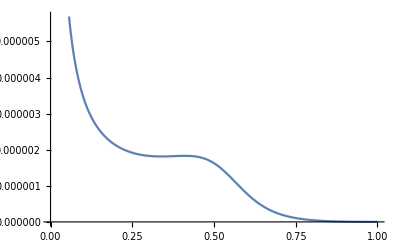

```mathematica
Plot[f[s0*x],{x,0,1}]
```

```mathematica
Plo
```

-Graphics-